```mathematica
SetDirectory["/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete/mag"]
fileList=FileNames[];
Length[fileList]
tot=28
Monitor[data=Table[Import[fileList[[i+tot*(j-1)]],"Data"][[2;;All,1]],{i,1,tot},{j,1,tot}];,{i,j}]
Dimensions[data]
```

/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete/test2

1569

28

{28,28,490}

```mathematica
Sqrt[1568/2]
```

28

```mathematica
{If[data[[2,2,60]]>20,1,0],If[data[[2,2,140]]>20,1,0],If[data[[2,2,220]]>20,1,0]}
```

{1,1,1}

```mathematica
{1,1,1}
```

```mathematica
{1,1,1}
```

{1,1,1}

```mathematica
isGate[data_,thresh_]:=Block[{seg},
seg={If[data[[60]]>thresh,1,0],If[data[[140]]>thresh,1,0],If[data[[220]]>20,1,0],If[data[[300]]>thresh,1,0]};
Piecewise[{
{1,seg=={1,1,1,1}},
{2,seg=={1,1,1,0}},
{3,seg=={0,1,1,0}},
{4,seg=={1,0,0,0}},
{5,seg=={0,1,1,1}},
{6,seg=={1,0,0,1}},
{7,seg=={0,0,0,1}},
{8,seg=={0,0,0,0}}
}]
]

dat=Table[isGate[data[[i,j]],1],{i,1,tot},{j,1,tot}]
```

{{8,8,8,8,8,4,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,4,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,4,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,4,4,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,4,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,4,0,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,4,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,4,6,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,7,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,3,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,5,3,5,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,5,5,3,3,5,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,5,3,3,5,5,5,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,5,3,3,3,5,5,5,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,5,3,5,3,3,3,5,5,5,5,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,5,5,3,3,3,3,5,5,5,5,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,3,3,5,3,3,3,3,3,5,5,5,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,3,3,3,3,3,0,5,8,3,5,5,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,3,8,0,3,0,8,8,8,3,3,5,5,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,8,8,0,8,8,8,0,3,3,3,3,5,5,5,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,0,3,0,3,3,3,5,5,5,1,1,1},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,0,0,3,0,0,8,3,3,0,5,1,1},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,0,8,8,0,8,0,5,1,5},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,0,0,5,2},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,3,3,3},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,0,3},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,0}}

```mathematica
ListPlot[data[[20,20]]]
```

Part::partw: Part 20 of {«1»} does not exist.

ListPlot::lpn: «1» is not a list of numbers or pairs of numbers.

ListPlot[{{1},{1},{1},{1},{1},{1},{1},{1}}⟦20,20⟧]
 |  |  |  |

0.65

RGBColor[0.8, 0.1, 0.1]

RGBColor[0.9, 0.5, 0.2]

RGBColor[0.9, 0.8, 0.3]

RGBColor[0.1, 0.8, 0.4]

RGBColor[0.1, 0.4, 0.8]

RGBColor[0.7, 0.4, 0.8]

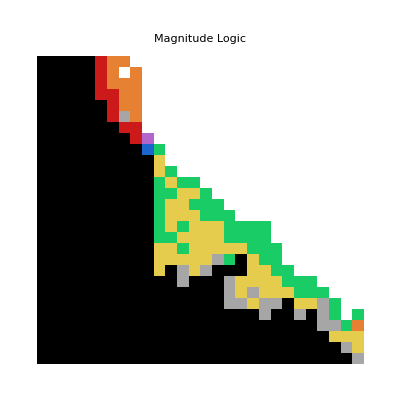

```mathematica
grey=.65
red = RGBColor[.8,.1,.1]
orange=  RGBColor[.9,.5,.2]
yellow=RGBColor[.9,.8,.3]
green= RGBColor[.1,.8,.4]
blue =RGBColor[.1,.4,.8]
purple=RGBColor[.7,.4,.8]

ArrayPlot[dat,ColorRules->
{8->Black,1->White,4->red,2->orange,3->yellow,5->green,7->blue,6->purple,0->GrayLevel[grey],"NIMP1"->GrayLevel[grey],"NIMP2"->GrayLevel[grey],"AIMP1"->GrayLevel[grey],"AIMP2"->GrayLevel[grey],"XIMP1"->GrayLevel[grey],"XIMP2"->GrayLevel[grey],"IMP1"->GrayLevel[grey],"IMP2"->GrayLevel[grey]},PlotLegends->Automatic,DataRange->{{1.5,4.5},{-2.5,0.5}},FrameTicks->Automatic,FrameLabel->{"Inhibitory Bias","Excitatory Bias"},PlotLabel->Style["Magnitude Logic","Title",Black,24]]
```

```mathematica
Table[{i,j},{i,1,28},{j,1,28}];
isGate[data[[8,10]],1]
```

6

```mathematica
f={Position[dat,4],Position[dat,2]}
g={Position[dat,2],Position[dat,3]}
h1= {Position[dat,5],Position[dat,7]}
h2= {Position[dat,6],Position[dat,7]}
f[[1]]
Dimensions[f[[1]]]
```

{{{1,6},{2,6},{3,6},{4,6},{4,7},{5,7},{6,7},{7,8},{7,9},{8,9}},{{1,7},{1,8},{2,7},{2,9},{3,7},{3,8},{3,9},{4,8},{4,9},{5,8},{5,9},{6,9},{25,28}}}

{{{1,7},{1,8},{2,7},{2,9},{3,7},{3,8},{3,9},{4,8},{4,9},{5,8},{5,9},{6,9},{25,28}},{{10,11},{11,11},{12,12},{13,13},{13,14},{14,12},{14,13},{15,12},{15,13},{15,14},{16,12},{16,14},{16,15},{16,16},{17,13},{17,14},{17,15},{17,16},{18,11},{18,12},{18,14},{18,15},{18,16},{18,17},{18,18},{19,11},{19,12},{19,13},{19,14},{19,15},{19,19},{20,11},{20,14},{20,19},{20,20},{21,18},{21,19},{21,20},{21,21},{22,18},{22,20},{22,21},{22,22},{23,19},{23,23},{23,24},{26,26},{26,27},{26,28},{27,28}}}

{{{9,11},{11,12},{12,11},{12,13},{12,14},{13,11},{13,12},{13,15},{14,11},{14,14},{14,15},{14,16},{15,11},{15,15},{15,16},{15,17},{16,11},{16,13},{16,17},{16,18},{16,19},{16,20},{17,11},{17,12},{17,17},{17,18},{17,19},{17,20},{18,13},{18,19},{18,20},{18,21},{19,17},{19,20},{19,21},{20,21},{20,22},{21,22},{21,23},{21,24},{22,23},{22,24},{22,25},{23,26},{24,26},{24,28},{25,27}},{{9,10}}}

{{{8,10}},{{9,10}}}

{{1,6},{2,6},{3,6},{4,6},{4,7},{5,7},{6,7},{7,8},{7,9},{8,9}}

{10,2}

```mathematica
vdat=Table[Table[Import["/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete/test2/V_e_"<>IntegerString[f[[k,i,2]]-1, 10, 3]<>"_i_"<>IntegerString[f[[k,i,1]]-1, 10, 3]<>"","Table"][[2;;-1,1]],{i,1,Length[f[[k]]]}],{k,1,2}];
Dimensions[vdat[[1]]]

vgdat=Table[Table[Import["/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete/mag_V/V_e_"<>IntegerString[g[[k,i,2]]-1, 10, 3]<>"_i_"<>IntegerString[g[[k,i,1]]-1, 10, 3]<>"","Table"][[2;;-1,1]],{i,1,Length[g[[k]]]}],{k,1,2}];
Dimensions[vdat[[1]]]
vh1dat=Table[Table[Import["/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete/mag_V/V_e_"<>IntegerString[h1[[k,i,2]]-1, 10, 3]<>"_i_"<>IntegerString[h1[[k,i,1]]-1, 10, 3]<>"","Table"][[2;;-1,1]],{i,1,Length[h1[[k]]]}],{k,1,2}];
Dimensions[vdat[[1]]]
vh2dat=Table[Table[Import["/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete/mag_V/V_e_"<>IntegerString[h2[[k,i,2]]-1, 10, 3]<>"_i_"<>IntegerString[h2[[k,i,1]]-1, 10, 3]<>"","Table"][[2;;-1,1]],{i,1,Length[h2[[k]]]}],{k,1,2}];
Dimensions[vdat[[1]]]
```

{10,49000}

```mathematica
Stats[x_]:={Mean[x],StandardDeviation[x]}
Time=Table[1.Stats[Table[FindPeaks[vdat[[k,i,4000;;10000]],0,0.,-.04][[1,1]],{i,1,Length[f[[k]]]}]]
,{k,1,2}]
Timeg=Table[1.Stats[Table[FindPeaks[vgdat[[k,i,12000;;16000]],0,0.,-.04][[1,1]],{i,1,Length[g[[k]]]}]]
,{k,1,2}]
Timeh1=Table[1.Stats[Table[FindPeaks[vh1dat[[k,i,8000;;12000]],0,0.,-.04][[1,1]],{i,1,Length[g[[k]]]}]]
,{k,1,2}]
Timeh2=Table[1.Stats[Table[FindPeaks[vh2dat[[k,i,16000;;20000]],0,0.,-.04][[1,1]],{i,1,Length[g[[k]]]}]]
,{k,1,2}]
```

{{555.4,87.7334},{387.692,225.91}}

{{369.769,203.427},{584.66,176.443}}

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 8000 through 12000 in $Failed⟦2;;-1,1⟧.

FindPeaks::arg: The argument {{{-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,«48990»},{-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,«48990»},«8»,«3»},{{-0.07,«9»,«48990»},«9»,«40»}}⟦«1»⟧ at position 1 is not a consistent list of real values.

Part::take: Cannot take positions 8000 through 12000 in $Failed⟦2;;-1,1⟧.

FindPeaks::arg: The argument {{{-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,«48990»},{-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,«48990»},«8»,«3»},{{-0.07,«9»,«48990»},«9»,«40»}}⟦«1»⟧ at position 1 is not a consistent list of real values.

Part::take: Cannot take positions 8000 through 12000 in $Failed⟦2;;-1,1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

FindPeaks::arg: The argument {{{-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,«48990»},{-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,«48990»},«8»,«3»},{{-0.07,«9»,«48990»},«9»,«40»}}⟦«1»⟧ at position 1 is not a consistent list of real values.

General::stop: Further output of FindPeaks::arg will be suppressed during this calculation.

Mean::rectt: Rectangular array expected at position 1 in Mean[<<807226560 bytes>>].

StandardDeviation::rectt: Rectangular array expected at position 1 in StandardDeviation[<<807226560 bytes>>].

$Aborted

Part::take: Cannot take positions 16000 through 20000 in $Failed⟦2;;-1,1⟧.

FindPeaks::arg: The argument {{{-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,-0.07,«48990»},$Failed⟦2;;-1,1⟧,$Failed⟦2;;-1,1⟧,$Failed⟦2;;-1,1⟧,«1»,«1»,«1»,$Failed⟦2;;-1,1⟧,$Failed⟦2;;-1,1⟧,$Failed⟦2;;-1,1⟧,«3»},«1»}⟦«1»⟧ at position 1 is not a consistent list of real values.

Part::take: Cannot take positions 16000 through 20000 in $Failed⟦2;;-1,1⟧.

$Aborted[]

Part::take: Cannot take positions 16000 through 20000 in $Failed⟦2;;-1,1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

{{555.4,87.7334},{387.692,225.91},{369.769,203.427},{584.66,176.443}}

{And 1,1,Or 1,1,Or 1,0,XOR 0,1}

{555.4→87.7334,387.692→225.91,369.769→203.427,584.66→176.443}

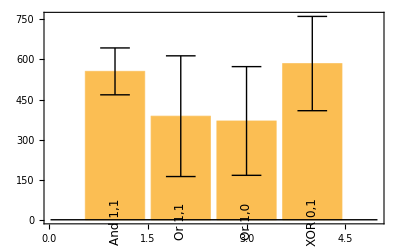

```mathematica
bardat=Join[Time,Timeg]
labels={"And 1,1","Or 1,1","Or 1,0","XOR 0,1"}
chartdat=Table[bardat[[i,1]]->bardat[[i,2]],{i,1,4}]

errorBar[type_:"Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]

BarChart[chartdat,ChartElementFunction->errorBar["Rectangle"],ChartLabels->Placed[labels,Axis,Rotate[Style[#,12,FontFamily->"Arial"],Pi/2]&],Frame->Left,FrameLabel->Automatic]
```

```mathematica
vdat[[1]]
```

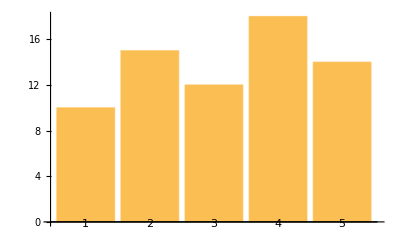

Show::gcomb: Could not combine the graphics objects in Show[,ErrorListPlot[{{1,10,{1,1.2}},{2,15,{2,2.3}},{3,12,{3,1.7}},{4,18,{4,2.8}},{5,14,{5,1.3}}},PlotStyle→None,Filling→Axis]].

Show[-Graphics-,ErrorListPlot[{{1,10,{1,1.2}},{2,15,{2,2.3}},{3,12,{3,1.7}},{4,18,{4,2.8}},{5,14,{5,1.3}}},PlotStyle→None,Filling→Axis]]

```mathematica
data={{1,10,1},{2,15,2},{3,12,1.5},{4,18,2.5},{5,14,1}};
errors={{1,1.2},{2,2.3},{3,1.7},{4,2.8},{5,1.3}};
errorBarData=Transpose[{data[[All,1]],data[[All,2]],errors}];
barChart=BarChart[data[[All,2]],ChartLabels->data[[All,1]]]
errorBarChart=Show[barChart,ErrorListPlot[Transpose[{data[[All,1]],data[[All,2]],errors}],PlotStyle->None,Filling->Axis]]
```

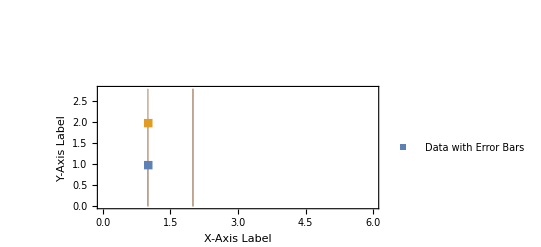

```mathematica
ListPlot[errorBarData,PlotStyle->PointSize[Large],PlotMarkers->"■",Filling->Axis,Joined->False,PlotRange->{{0,6},All},Frame->True,FrameLabel->{"X-Axis Label","Y-Axis Label"},PlotLegends->{"Data with Error Bars"}]
```